# Tarea 3

## Método de Newton-Raphson

Primero definimos la función a resolver. De la cual se desean encontrar las raíces: f(x)= x^2 - Cos[x]

```mathematica
f[x_]:=x^2-Cos[x];
```

Se define un función que realiza un paso en el método de Newton-Raphson:

```mathematica
NewRaStep[x_]:=x-f[x]/f'[x];
```

```mathematica
NewRaStep[0.5]
```

0.924207

Repitiendo el procedimiento n veces y guardando las soluciones se obtienen las iteraciones del método de NR:

```mathematica
NewRap[x0_,n_]:=Block[{soluciones={x0},x=x0},
Do[
x=NewRaStep[x];
AppendTo[soluciones,x]; 
(*Se añade le nuevo valor de x a la lista*)
,
n 
(*Número de repeticiones*)
 ];
 soluciones
];
```

```mathematica
listadesoluciones=NewRap[0.2,10]
```

{0.2,1.77026,1.03321,0.843334,0.824335,0.824132,0.824132,0.824132,0.824132,0.824132,0.824132}

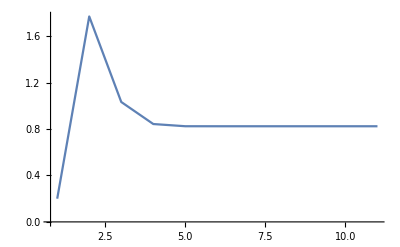

```mathematica
ListLinePlot[listadesoluciones,PlotRange-> All]
```

Definir la función para medir la razón de errores entre pasos, evaluar en los puntos de la lista de soluciones y graficar.

```mathematica
NRError= -f''[#]/(2 f'[#])&
```

-f''[#1]/(2 f'[#1])&

```mathematica
Map[NRError,{listadesoluciones}]
```

{{-2.48891,-0.19929,-0.429357,-0.547553,-0.562172,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331,-0.562331}}